# Refractory Period Model

## Preface

Everything in the preface is meant to be general code that should be applicable to any notebook.In most cases,this section will house commands/scripts that add functionality to the notebook,regardless of the content of the notebook

## Input cell folding

The following code is a script that adds a button to turn all input cells off,thereby just showing the plots,outputs,and/or manipulators.

```mathematica
ShowInputCells[sh_]:=SetOptions[#,CellOpen->sh]&/@Cells[EvaluationNotebook[],CellStyle->{"Input"}]

SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[DynamicModuleBox[{showHide$$=True},TemplateBox[{"\"Show/hide input cells \"",CheckboxBox[Dynamic[showHide$$,{(showHide$$=#)&,ShowInputCells[showHide$$]&}]]},"RowDefault"],DynamicModuleValues:>{}]],"Output"]]
```

## Workspace

## Function Definitions

### Conversion functions between i_in and I_in or I_lk

IintoiIn is also the equivalent of defining i_in as a function of dimensional units (I_in, I_lk, ρ_qua, and  ρ_ilkr)

```mathematica
IintoiIn[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
iIntoIin[iIn_,Ilk_,pqua_,pilkr_]:=(iIn (Ilk+pilkr)^2)/(pqua Ilk)
iIntoIlkP[iIn_,Iin_,pqua_,pilkr_]:=(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
iIntoIlkN[iIn_,Iin_,pqua_,pilkr_]:=(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)
```

#### Derivation of the relation between i_in and I_in or I_lk

Solve for I_in or I_lk in terms of i_in, I_lk/I_in (respectively), ρ_qua, and ρ_ilkr.  These solve equations were used to get the values for iIntoIlkP and iIntoIlkN above.

```mathematica
Solve[pqua (Iin Ilk)/(Ilk+pilkr)^2==iIn,Iin]
Solve[pqua (Iin Ilk)/(Ilk+pilkr)^2==iIn,Ilk]
```

{{Iin→(iIn (Ilk+pilkr)^2)/(Ilk pqua)}}

{{Ilk→(-√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)},{Ilk→(√(Iin^2 pqua^2-4 iIn Iin pilkr pqua)-2 iIn pilkr+Iin pqua)/(2 iIn)}}

#### Test Plot showing I_in to I_lk relation for a given value of i_in

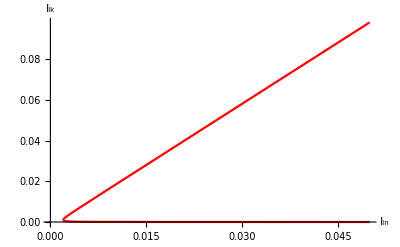

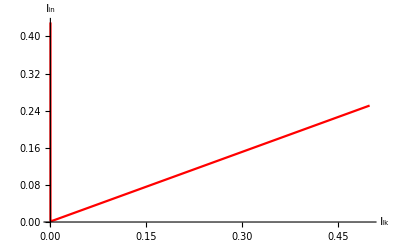

```mathematica
tmpiIn=1.0;
Plot[{iIntoIlkP[tmpiIn,Iin,pquatmp,pilkrtmp],iIntoIlkN[tmpiIn,Iin,pquatmp,pilkrtmp]},{Iin,0,0.05},PlotStyle->Red,AxesLabel->{"I_in","I_lk"}]
Plot[{iIntoIin[tmpiIn,Ilk,pquatmp,pilkrtmp]},{Ilk,0,0.5},PlotStyle->Red,AxesLabel->{"I_lk","I_in"}]
```

### Soma functions

#### τ as a function of I_lk, ρ_ilkr, and ρ_tau

```mathematica
τ[Ilk_,ptau_,pilkr_]:=ptau/(Ilk+pilkr)
```

#### t_ref as a function of I_ref,ρ_ref

```mathematica
tref[Iref_,pref_]:=pref/Iref
```

#### h(i_in) Functions

```mathematica
h[iIn_,β0_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]-ArcTan[(β0-1)/(√(2 iIn-1))]))/(√(2 iIn-1))
hβ0[iIn_,β0_]:=(π-2ArcTan[(β0-1)/(√(2 iIn-1))])/(√(2 iIn-1))
hβf[iIn_,βf_]:=(2 (ArcTan[(βf-1)/(√(2 iIn-1))]+ArcCot[√(2 iIn-1)]))/(√(2 iIn-1))
h[iIn_]:=(π+2ArcCot[√(2 iIn-1)])/(√(2 iIn-1))
```

### Firing rate equations

#### Firing rate without refractory period, f_0

f_0=1/(τ·h(i_in)); τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2

```mathematica
f0[iIn_,τ_]=1/(τ h[iIn]);
f0[iIn_,β0_,βf_,τ_]=1/(τ h[iIn,β0,βf]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_]=1/(τ[Ilk,ptau,pilkr] h[IintoiIn[Iin,Ilk,pqua,pilkr]]);
f0[Iin_,Ilk_,pqua_,ptau_,pilkr_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[IintoiIn[Iin,Ilk,pqua,pilkr],β0,βf]);
```

#### Firing rate with refractory period, f

f=1/(τ·h(i_in)-t_ref)τ=ρ_tau/(I_lk+ρ_ilkr), h(i_in) is expanded as per some of the h functions above, i_in=(ρ_qua(I_in I_lk))/(I_lk+ρ_ilkr)^2, t_ref=ρ_ref/I_ref

```mathematica
f[iIn_,τ_,tref_]=1/(τ h[iIn]-tref);
f[iIn_,β0_,βf_,τ_,tref_]=1/(τ h[iIn,β0,βf]-tref);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_]=1/(τ[Ilk,ptau,pilkr] h[IintoiIn[Iin,Ilk,pqua,pilkr]]-tref[Iref,pref]);
f[Iin_,Ilk_,Iref_,pqua_,ptau_,pilkr_,pref_,β0_,βf_]=1/(τ[Ilk,ptau,pilkr] h[IintoiIn[Iin,Ilk,pqua,pilkr],β0,βf]-tref[Iref,pref]);
```

### Other Functions

### Thermal voltage, U_t, function

This function calculates the thermal voltage assuming that the input is given in Celsius

```mathematica
UtFunc[T_]:=QuantityMagnitude[UnitSimplify[UnitConvert[Quantity[T,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"]/Quantity["ElementaryCharge"]]];
```

### Leakage term in I_DS equation

ΛFunc  is a helper function that accepts the base leakage current of a device and multiplies it by the W/L ratio of a given transistor device

```mathematica
ΛFunc[W_,L_]:=W/L
```

### Refractory capacitor’s standing voltage, V_r

V_r is the voltage at the node that the refractory period’s capacitor charges/discharges.  This node is also the gate of the transistor that feeds into I_lk

```mathematica
Vr[Vin_,Vdd_,Vm_,Ut_,κ_,Λlkr_,Λbk_]:=Vdd+Vin-Vm+Ut/κ (Log[Λlkr/Λbk (1-ⅇ^((Vm-Vdd)/Ut))])
```

#### Derivation of the V_r

The equation above is superficially (b/c of some assumptions that I make) derived as follows:
Basic equations:
	I_l/α_7=I_lk/α_B1 , current mirror mirroring the leak current
	(I_m I_b)/(α_1 α_10)=(I_lk I_in)/(α_B1 α_B2), using translinear principle to use the biases (I_in and I_lk) to set the output (I_m)
	I_fb/α_4=I_m/α_3, this derivation assumes that transisor A_6 isn’t in the circuit and therefore I_fb is just a mirrored version of I_m
	I_r/α_12=I_ref/α_B3, current mirror for the refractory current
	I_lr=α_8 I_0 ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t)), because this transistor could/would be operating in the linear region during the refractory period
Derivation:
During the refractory period, we can assume capacitor C_m is charging or fully charged as long as the following condition is true:

(1)	I_l+I_lr>I_b+I_fb

Subsituting from the basic equations above:

	α_7/α_B1 I_lk+I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m+α_4/α_3 I_m
	I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m+α_4/α_3 I_m-α_7/α_B1 I_lk
	
Our first major assumption is that α_4/α_3 I_m and α_7/α_B1 I_lk can be ignored because during the refractory period I_m is small and therefore the (α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m dominates.

(2)	I_lr>(α_1 α_10)/(α_B1 α_B2)(I_lk I_in)/I_m, it should be noted here that this is the same as saying I_lr>I_b
	I_m I_lr>(α_1 α_10)/(α_B1 α_B2)I_lk I_in
	α_1 I_0 ⅇ^((-κ·V_mgs)/U_t)α_8 I_0 ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t))>(α_1 α_10)/(α_B1 α_B2)α_B1 I_0 ⅇ^((-κ·V_lkgs)/U_t)α_B2 I_0 ⅇ^((-κ·V_ings)/U_t), expand out the forms of I_x
	ⅇ^((-κ·V_mgs)/U_t)ⅇ^((-κ·V_lrgs)/U_t)(1-ⅇ^(V_lrds/U_t))>α_10/α_8 ⅇ^((-κ·V_lkgs)/U_t)ⅇ^((-κ·V_ings)/U_t), simplify out all of the constants on both sides of the equation
	ⅇ^((-κ·(V_mgs+V_lrgs))/U_t)(1-ⅇ^(V_lrds/U_t))>α_10/α_8 ⅇ^((-κ·(V_lkgs+V_ings))/U_t)
	(-κ·(V_mgs+V_lrgs))/U_t+log(1-ⅇ^(V_lrds/U_t))>log(α_10/α_8)+(-κ·(V_lkgs+V_ings))/U_t, take the log of both sides
	(-κ·(V_mgs+V_lrgs))/U_t>(-κ·(V_lkgs+V_ings))/U_t+log(α_10/α_8)-log(1-ⅇ^(V_lrds/U_t))
	(κ·(V_mgs+V_lrgs))/U_t<(κ·(V_lkgs+V_ings))/U_t-log(α_10/α_8)+log(1-ⅇ^(V_lrds/U_t))

(3)	V_mgs+V_lrgs<V_lkgs+V_ings+U_t/κ log(α_8/α_10(1-ⅇ^((V_m-V_dd)/U_t)))

#### Double check the derivation of V_r

Using the expanded form of I_lr>I_b, the essential result of Eq. 2 above, we try to apply the Solve function below to see if the derivation above matches what Mathematica solves for.

```mathematica
Solve[α8*E^((κ (Vdd-Vr))/Ut) (1-E^((Vm-Vdd)/Ut))==α10*E^((κ (Vm-Vin))/Ut),Vr]
```

{{Vr→ConditionalExpression[(κ Vdd-Ut (log(-(α10 ⅇ^(-(κ (Vin-Vm))/Ut))/(α8 ⅇ^(Vm/Ut-Vdd/Ut)-α8))+2 ⅈ π c_1))/κ,c_1∈ℤ]}}

This results in basically the same result as above.  The only reason for the basically clause is because of the conditional expression.  The conversion from the answer given by
the Solve function to the form I derived is written below.

	V_r=(κ V_dd-U_t (log(-(α_10 ⅇ^(-(κ (V_in-V_m))/U_t))/(α_8 ⅇ^((Vm-V_dd)/U_t)-α_8))+2 ⅈ π c_1))/κ
	V_r=V_dd-U_t/κ(log((α_10 ⅇ^(-(κ (V_in-V_m))/U_t))/(α_8-α_8 ⅇ^((Vm-V_dd)/U_t)))+(2 ⅈ π c_1)/κ)
	V_r=V_dd-U_t/κ(log((α_10 ⅇ^(-(κ (V_in-V_m))/U_t))/(α_8(1- ⅇ^((Vm-V_dd)/U_t))))+(2 ⅈ π c_1)/κ)
	V_r=V_dd+U_t/κ(log((α_8(1- ⅇ^((Vm-V_dd)/U_t)))/(α_10 ⅇ^(-(κ (V_in-V_m))/U_t)))+(2 ⅈ π c_1)/κ)
	V_r=V_dd+U_t/κ(log(α_8/α_10(1- ⅇ^((Vm-V_dd)/U_t)))-log( ⅇ^(-(κ (V_in-V_m))/U_t))+(2 ⅈ π c_1)/κ)
	V_r=V_dd+U_t/κ log(α_8/α_10(1- ⅇ^((Vm-V_dd)/U_t)))-U_t/κ log( ⅇ^(-(κ (V_in-V_m))/U_t))+ (2 U_t ⅈ π c_1)/κ^2)
	V_r=V_dd+U_t/κ log(α_8/α_10(1- ⅇ^((Vm-V_dd)/U_t)))+U_t/κ(κ (V_in-V_m))/U_t+ (2 U_t ⅈ π c_1)/κ^2)
	V_r=V_dd+U_t/κ log(α_8/α_10(1- ⅇ^((Vm-V_dd)/U_t)))+ (V_in-V_m)+ (2 U_t ⅈ π c_1)/κ^2)

V_r=V_dd+V_in-V_m+U_t/κ log(α_8/α_10(1- ⅇ^((Vm-V_dd)/U_t)))+ (2 U_t ⅈ π c_1)/κ^2)

## Refractory Period Model

### Manipulator varying V_r as a function of the temperature, V_in, and V_m (membrane voltage)

```mathematica
Manipulate[
Vr[vin,vdd,vm,UtFunc[temp],κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]],
{{temp,25,"temp"},20,30,1,Appearance->{"Labeled","Open"}},
{{vin,1.21479,"V_in"},1.1,1.3,0.00001,Appearance->{"Labeled","Open"}},
{{vm,1.7999,"V_m"},1.5,1.8,0.01,Appearance->{"Labeled","Open"}}
]/.{vdd->1.8,κ1->0.7}
```

### Some other manipulator

```mathematica
Manipulate[
Grid[{{
Show[
Plot[
{
Vr[vin,vdd,vmSlide,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]],
1.8
},{vin,xMin1,xMax1},
PlotRange->{0.1,2.},
ImageSize->300,AxesLabel->{"V_in","V_r"}],
ListPlot[{
{vinSlide,Vr[vinSlide,vdd,vmSlide,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]]}
},
PlotMarkers->{Automatic,Medium}
]],
Show[
Plot[
{
Vr[vinSlide,vdd,vm,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]]
},{vm,xMin2,xMax2},
PlotRange->{0.1,2.},
ImageSize->300,AxesLabel->{"V_m","V_r"}],
ListPlot[
{
{vmSlide,Vr[vinSlide,vdd,vmSlide,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]]}
},
PlotMarkers->{Automatic,Medium}
]]
},{
Show[
Plot3D[
{
Vr[vin,vdd,vm,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]]
},{vin,xMin1,xMax1},{vm,xMin2,xMax2},
PlotRange->{0.1,2.},
ImageSize->600,AxesLabel->{"V_in","V_m","V_r"}] ,
ListPointPlot3D[
{
{vinSlide,vmSlide,Vr[vinSlide,vdd,vmSlide,ϕt,κ1,ΛFunc[5.4*10^-7,4*10^-7],ΛFunc[6.5*10^-7,4.33*10^-6]]}
},Filling->Top,PlotRange->{0.1,2.},ImageSize->600,AxesLabel->{"V_in","V_m","V_r"}
]
],SpanFromLeft}}],
{{xMin1,1.2,"x_min1"},0,1.8,1.×10^-13,Appearance->{"Labeled","Open"}},
{{xMax1,1.8,"x_max1"},0,1.8,0.001,Appearance->{"Labeled","Open"}},
{{xMin2,1.65,"x_min2"},0,1.8,1.×10^-13,Appearance->{"Labeled","Open"}},
{{xMax2,1.8,"x_max2"},0,1.8,0.001,Appearance->{"Labeled","Open"}},
{{yMin,0,"y_min"},0,1.8,0.1,Appearance->{"Labeled","Open"}},
{{vinSlide,1.21479,"V_in"},1.1,1.3,0.00001,Appearance->{"Labeled","Open"}},
{{vmSlide,1.7999,"V_m"},1.5,1.8,0.01,Appearance->{"Labeled","Open"}}
(*{{temp,25,"temp"},20,30,1,Appearance->{"Labeled","Open"}}*)
]/.{vdd->1.8,κ1->0.7,ϕt->UtFunc[25]}
```

## Appendix/Scratchpad

## Old work that I can’t remember the reason for having implemented

### Manipulator varying f_0 as a function of I_lk

The following manipulator allows the user to vary any of the biases and ρ_vals to calculate other paramteters in the system.  It also visualizes this curve.

```mathematica
DynamicModule[{Ic=0.357569,Il=0.118759,Iref=1000.25,pqua=1.02664,pilkr=-0.00376201, ptau=0.0004599,τlo=.002, τhi=.040,vinlo=0.5, vinhi=20,  freqlo=20, freqhi=220},
Grid[{
{Grid[{
{"Input Variables",SpanFromLeft,SpanFromLeft},
{"I_c",InputField[Dynamic[Ic]],Dynamic[Ic],"ρ_qua",InputField[Dynamic[pqua]],Dynamic[pqua]},
{"I_l",InputField[Dynamic[Il]],Dynamic[Il],"ρ_tau",InputField[Dynamic[ptau]],Dynamic[ptau]},
{"","","","ρ_ilkr",InputField[Dynamic[pilkr]],Dynamic[pilkr]}
(*{"I_ref",Slider[Dynamic[Iref],{1.25,50,.25}],Dynamic[Iref]},*)
},Alignment->{Center},Dividers->{False,{2->True}}]},
{Grid[{
{"\nInput Ranges",SpanFromLeft,SpanFromLeft},
{"τ_lo",Slider[Dynamic[τlo],{0,.01,.001}],Dynamic[τlo],"τ_hi",Slider[Dynamic[τhi],{.03,.05,.005}],Dynamic[τhi]},
{"v_in_lo",Slider[Dynamic[vinlo],{0.5,1,0.1}],Dynamic[vinlo],"v_in_hi",Slider[Dynamic[vinhi],{15,25,1}],Dynamic[vinhi]},
{"f_lo",Slider[Dynamic[freqlo],{0,50,5}],Dynamic[freqlo],"f_hi",Slider[Dynamic[freqhi],{150,250,5}],Dynamic[freqhi]}
},Alignment->{Center},Dividers->{False,{2->True}}]},
{Grid[{
{"\nLimits",SpanFromLeft,SpanFromLeft},
{"τ_m",Dynamic[First[FindRoot[τ[ptau,pilkr,Ilx]==τlo,{Ilx,0.01}]]],Dynamic[τlo*1000],"ms",Dynamic[First[FindRoot[τ[Ilx,ptau,pilkr]==τhi,{Ilx,0.01}]]],Dynamic[τhi*1000],"ms"},
{"v_in",Dynamic[First[FindRoot[IintoiIn[Ic,Ilx,pqua,pilkr]==vinlo,{Ilx,0.001}]]],Dynamic[vinlo],"V",Dynamic[First[FindRoot[IintoiIn[Ic,Ilx,pqua,pilkr]==vinhi,{Ilx,0.001}]]],Dynamic[vinhi],"V"},
{"f_0",Dynamic[First[FindRoot[f0[IintoiIn[Ic,Ilx,pqua,pilkr],τ[Ilx,ptau,pilkr]]==freqlo,{Ilx,0.1}]]],Dynamic[freqlo],"Hz",Dynamic[First[FindRoot[f0[IintoiIn[Ic,Ilx,pqua,pilkr],τ[Ilx,ptau,pilkr]]==freqhi,{Ilx,0.1}]]],Dynamic[freqhi],"Hz"}
},Alignment->{Center},Dividers->{False,{2->True}}]},
{Grid[{
{"\nOutput Values",SpanFromLeft,SpanFromLeft},
{"τ_m:",Panel[Dynamic[τ[Il,ptau,pilkr]],Background->LightGray],Panel[Dynamic[1000τ[Il,ptau,pilkr]],Background->LightGray], "ms"},
{"v_in:",Panel[Dynamic[IintoiIn[Ic,Il,pqua,pilkr]],Background->LightGray],"h(v_in):",Panel[Dynamic[h[IintoiIn[Ic,Il,pqua,pilkr]]],Background->LightGray]},
{"f_0:",Panel[Dynamic[f0[IintoiIn[Ic,Il,pqua,pilkr],τ[Il,ptau,pilkr]]],Background->LightGray]}
},Alignment->{Center},Dividers->{False,{2->True}}]},
{Grid[{
{Dynamic[Plot[{f0[IintoiIn[Ic,Ilx,pqua,pilkr],τ[Ilx,ptau,pilkr]],freqlo,freqhi,150},{Ilx, 0,1} ,
ImageSize->400,
PlotRange->{0,All},
AxesLabel->{"I_l","f_0"}
]]}
},Alignment->{Center},Dividers->{False,{2->True}}]}
},Dividers->{False,{2->True}}]
]
```

### Plot f_0 as a function of I_lk

```mathematica
tauVals = {0.002,0.004,0.006,0.008,0.010,0.012,0.014,0.016,0.018}
Ils=(.0004599)/tauVals-(-0.00376201)
```

{0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018}

{0.233712,0.118737,0.080412,0.0612495,0.049752,0.042087,0.036612,0.0325058,0.029312}

```mathematica
Ics = {0.30499571,0.35756891,0.43493242,0.51596424,0.59684306,0.67641998,0.75427569,0.83025377,0.90430951}
```

{0.304996,0.357569,0.434932,0.515964,0.596843,0.67642,0.754276,0.830254,0.90431}

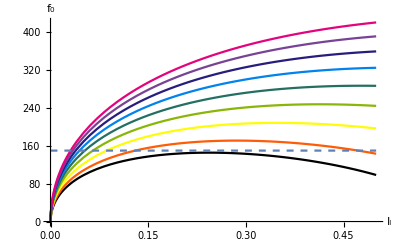
-Graphics- | (Tau | Il | Ic
0.002 | 0.233712 | 0.304996
0.004 | 0.118737 | 0.357569
0.006 | 0.080412 | 0.434932
0.008 | 0.0612495 | 0.515964
0.01 | 0.049752 | 0.596843
0.012 | 0.042087 | 0.67642
0.014 | 0.036612 | 0.754276
0.016 | 0.0325058 | 0.830254
0.018 | 0.029312 | 0.90431)

```mathematica
legendInfo =Transpose[{ Prepend[tauVals,"Tau"],Prepend[Ils,"Il"],Prepend[Ics,"Ic"]}];
Grid[{{
Show[
Plot[{
f0[IintoiIn[Ics⟦1⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦2⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦3⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦4⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦5⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦6⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦7⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦8⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]],
f0[IintoiIn[Ics⟦9⟧,Ilx,1.02664,0.00376201],τ[Ilx,0.0004599,0.00376201]]
},
{Ilx, 0,0.5},
ImageSize->400,AxesLabel->{"I_l","f_0"},PlotLegends->Ils,
PlotStyle->ColorData[3,"ColorList"]
],
Plot[150,{Ilx,0,0.5}, PlotStyle->Dashed]
],
legendInfo
}}]
```

### Some calculation that has something to do with refractory period

```mathematica
ρref=.0221613115123;
irefInv = Range[.01,.4,.03] 
irefs=1/irefInv
implementedTrefs=ρref/irefs
```

{0.01,0.04,0.07,0.1,0.13,0.16,0.19,0.22,0.25,0.28,0.31,0.34,0.37,0.4}

{100.,25.,14.2857,10.,7.69231,6.25,5.26316,4.54545,4.,3.57143,3.22581,2.94118,2.7027,2.5}

{0.000221613,0.000886452,0.00155129,0.00221613,0.00288097,0.00354581,0.00421065,0.00487549,0.00554033,0.00620517,0.00687001,0.00753485,0.00819969,0.00886452}

```mathematica
trefs=Range[.00005,.02,.001]
theoryIrefs=ρref/trefs
```

{0.00005,0.00105,0.00205,0.00305,0.00405,0.00505,0.00605,0.00705,0.00805,0.00905,0.01005,0.01105,0.01205,0.01305,0.01405,0.01505,0.01605,0.01705,0.01805,0.01905}

{443.226,21.106,10.8104,7.266,5.47193,4.38838,3.66303,3.14345,2.75296,2.44876,2.20511,2.00555,1.83911,1.69818,1.57732,1.47251,1.38077,1.29978,1.22777,1.16332}

```mathematica
firingRateRange = Range[20,27, 1/3]
```

{20,61/3,62/3,21,64/3,65/3,22,67/3,68/3,23,70/3,71/3,24,73/3,74/3,25,76/3,77/3,26,79/3,80/3,27}

```mathematica
Outer[Subtract, 1/firingRateRange, 1/firingRateRange]//N
```

(0. | 0.000819672 | 0.0016129 | 0.00238095 | 0.003125 | 0.00384615 | 0.00454545 | 0.00522388 | 0.00588235 | 0.00652174 | 0.00714286 | 0.00774648 | 0.00833333 | 0.00890411 | 0.00945946 | 0.01 | 0.0105263 | 0.011039 | 0.0115385 | 0.0120253 | 0.0125 | 0.012963
-0.000819672 | 0. | 0.000793231 | 0.00156128 | 0.00230533 | 0.00302648 | 0.00372578 | 0.00440421 | 0.00506268 | 0.00570207 | 0.00632319 | 0.00692681 | 0.00751366 | 0.00808444 | 0.00863979 | 0.00918033 | 0.00970664 | 0.0102193 | 0.0107188 | 0.0112056 | 0.0116803 | 0.0121433
-0.0016129 | -0.000793231 | 0. | 0.000768049 | 0.0015121 | 0.00223325 | 0.00293255 | 0.00361098 | 0.00426945 | 0.00490884 | 0.00552995 | 0.00613358 | 0.00672043 | 0.00729121 | 0.00784656 | 0.0083871 | 0.00891341 | 0.00942606 | 0.00992556 | 0.0104124 | 0.0108871 | 0.0113501
-0.00238095 | -0.00156128 | -0.000768049 | 0. | 0.000744048 | 0.0014652 | 0.0021645 | 0.00284293 | 0.0035014 | 0.00414079 | 0.0047619 | 0.00536553 | 0.00595238 | 0.00652316 | 0.00707851 | 0.00761905 | 0.00814536 | 0.00865801 | 0.00915751 | 0.00964436 | 0.010119 | 0.010582
-0.003125 | -0.00230533 | -0.0015121 | -0.000744048 | 0. | 0.000721154 | 0.00142045 | 0.00209888 | 0.00275735 | 0.00339674 | 0.00401786 | 0.00462148 | 0.00520833 | 0.00577911 | 0.00633446 | 0.006875 | 0.00740132 | 0.00791396 | 0.00841346 | 0.00890032 | 0.009375 | 0.00983796
-0.00384615 | -0.00302648 | -0.00223325 | -0.0014652 | -0.000721154 | 0. | 0.000699301 | 0.00137773 | 0.0020362 | 0.00267559 | 0.0032967 | 0.00390033 | 0.00448718 | 0.00505796 | 0.00561331 | 0.00615385 | 0.00668016 | 0.00719281 | 0.00769231 | 0.00817916 | 0.00865385 | 0.00911681
-0.00454545 | -0.00372578 | -0.00293255 | -0.0021645 | -0.00142045 | -0.000699301 | 0. | 0.000678426 | 0.0013369 | 0.00197628 | 0.0025974 | 0.00320102 | 0.00378788 | 0.00435866 | 0.004914 | 0.00545455 | 0.00598086 | 0.00649351 | 0.00699301 | 0.00747986 | 0.00795455 | 0.00841751
-0.00522388 | -0.00440421 | -0.00361098 | -0.00284293 | -0.00209888 | -0.00137773 | -0.000678426 | 0. | 0.000658472 | 0.00129786 | 0.00191898 | 0.0025226 | 0.00310945 | 0.00368023 | 0.00423558 | 0.00477612 | 0.00530244 | 0.00581508 | 0.00631458 | 0.00680144 | 0.00727612 | 0.00773908
-0.00588235 | -0.00506268 | -0.00426945 | -0.0035014 | -0.00275735 | -0.0020362 | -0.0013369 | -0.000658472 | 0. | 0.000639386 | 0.0012605 | 0.00186413 | 0.00245098 | 0.00302176 | 0.00357711 | 0.00411765 | 0.00464396 | 0.00515661 | 0.00565611 | 0.00614296 | 0.00661765 | 0.00708061
-0.00652174 | -0.00570207 | -0.00490884 | -0.00414079 | -0.00339674 | -0.00267559 | -0.00197628 | -0.00129786 | -0.000639386 | 0. | 0.000621118 | 0.00122474 | 0.00181159 | 0.00238237 | 0.00293772 | 0.00347826 | 0.00400458 | 0.00451722 | 0.00501672 | 0.00550358 | 0.00597826 | 0.00644122
-0.00714286 | -0.00632319 | -0.00552995 | -0.0047619 | -0.00401786 | -0.0032967 | -0.0025974 | -0.00191898 | -0.0012605 | -0.000621118 | 0. | 0.000603622 | 0.00119048 | 0.00176125 | 0.0023166 | 0.00285714 | 0.00338346 | 0.0038961 | 0.0043956 | 0.00488246 | 0.00535714 | 0.00582011
-0.00774648 | -0.00692681 | -0.00613358 | -0.00536553 | -0.00462148 | -0.00390033 | -0.00320102 | -0.0025226 | -0.00186413 | -0.00122474 | -0.000603622 | 0. | 0.000586854 | 0.00115763 | 0.00171298 | 0.00225352 | 0.00277984 | 0.00329248 | 0.00379198 | 0.00427884 | 0.00475352 | 0.00521648
-0.00833333 | -0.00751366 | -0.00672043 | -0.00595238 | -0.00520833 | -0.00448718 | -0.00378788 | -0.00310945 | -0.00245098 | -0.00181159 | -0.00119048 | -0.000586854 | 0. | 0.000570776 | 0.00112613 | 0.00166667 | 0.00219298 | 0.00270563 | 0.00320513 | 0.00369198 | 0.00416667 | 0.00462963
-0.00890411 | -0.00808444 | -0.00729121 | -0.00652316 | -0.00577911 | -0.00505796 | -0.00435866 | -0.00368023 | -0.00302176 | -0.00238237 | -0.00176125 | -0.00115763 | -0.000570776 | 0. | 0.00055535 | 0.00109589 | 0.00162221 | 0.00213485 | 0.00263435 | 0.00312121 | 0.00359589 | 0.00405885
-0.00945946 | -0.00863979 | -0.00784656 | -0.00707851 | -0.00633446 | -0.00561331 | -0.004914 | -0.00423558 | -0.00357711 | -0.00293772 | -0.0023166 | -0.00171298 | -0.00112613 | -0.00055535 | 0. | 0.000540541 | 0.00106686 | 0.0015795 | 0.002079 | 0.00256586 | 0.00304054 | 0.0035035
-0.01 | -0.00918033 | -0.0083871 | -0.00761905 | -0.006875 | -0.00615385 | -0.00545455 | -0.00477612 | -0.00411765 | -0.00347826 | -0.00285714 | -0.00225352 | -0.00166667 | -0.00109589 | -0.000540541 | 0. | 0.000526316 | 0.00103896 | 0.00153846 | 0.00202532 | 0.0025 | 0.00296296
-0.0105263 | -0.00970664 | -0.00891341 | -0.00814536 | -0.00740132 | -0.00668016 | -0.00598086 | -0.00530244 | -0.00464396 | -0.00400458 | -0.00338346 | -0.00277984 | -0.00219298 | -0.00162221 | -0.00106686 | -0.000526316 | 0. | 0.000512645 | 0.00101215 | 0.001499 | 0.00197368 | 0.00243665
-0.011039 | -0.0102193 | -0.00942606 | -0.00865801 | -0.00791396 | -0.00719281 | -0.00649351 | -0.00581508 | -0.00515661 | -0.00451722 | -0.0038961 | -0.00329248 | -0.00270563 | -0.00213485 | -0.0015795 | -0.00103896 | -0.000512645 | 0. | 0.0004995 | 0.000986355 | 0.00146104 | 0.001924
-0.0115385 | -0.0107188 | -0.00992556 | -0.00915751 | -0.00841346 | -0.00769231 | -0.00699301 | -0.00631458 | -0.00565611 | -0.00501672 | -0.0043956 | -0.00379198 | -0.00320513 | -0.00263435 | -0.002079 | -0.00153846 | -0.00101215 | -0.0004995 | 0. | 0.000486855 | 0.000961538 | 0.0014245
-0.0120253 | -0.0112056 | -0.0104124 | -0.00964436 | -0.00890032 | -0.00817916 | -0.00747986 | -0.00680144 | -0.00614296 | -0.00550358 | -0.00488246 | -0.00427884 | -0.00369198 | -0.00312121 | -0.00256586 | -0.00202532 | -0.001499 | -0.000986355 | -0.000486855 | 0. | 0.000474684 | 0.000937647
-0.0125 | -0.0116803 | -0.0108871 | -0.010119 | -0.009375 | -0.00865385 | -0.00795455 | -0.00727612 | -0.00661765 | -0.00597826 | -0.00535714 | -0.00475352 | -0.00416667 | -0.00359589 | -0.00304054 | -0.0025 | -0.00197368 | -0.00146104 | -0.000961538 | -0.000474684 | 0. | 0.000462963
-0.012963 | -0.0121433 | -0.0113501 | -0.010582 | -0.00983796 | -0.00911681 | -0.00841751 | -0.00773908 | -0.00708061 | -0.00644122 | -0.00582011 | -0.00521648 | -0.00462963 | -0.00405885 | -0.0035035 | -0.00296296 | -0.00243665 | -0.001924 | -0.0014245 | -0.000937647 | -0.000462963 | 0.)